```mathematica
∫_0^y x/(x^2 + yp^2)ⅆyp
```

ConditionalExpression[ArcTan[y/x],Re[x/y]≠0||Im[x/y]>1||Im[x/y]<-1]

```mathematica
∇_{x, y} ArcTan[y/x]
```

{-y/(x^2 (1+y^2/x^2)),1/(x (1+y^2/x^2))}

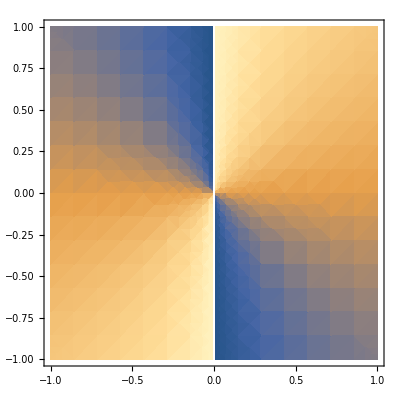

```mathematica
DensityPlot[ArcTan[y/x], {x, -1, 1}, {y, -1, 1}]
```

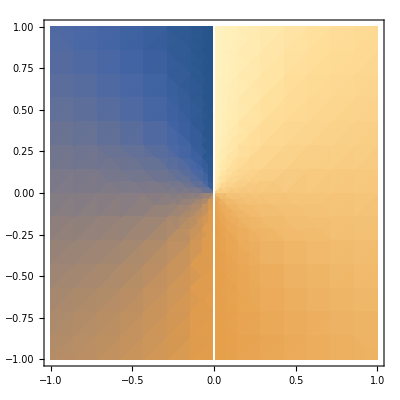

```mathematica
DensityPlot[If[x > 0, ArcTan[y/x] + π, ArcTan[y/x]], {x, -1, 1}, {y, -1, 1}]
```